```mathematica
(* Mathematica Sheet for Latin Hypercube Sampling for Parental Care*)

(*This defines the number of samples/bins to create*)
n=4000;
(*z =6;*)
(*cm=0.7;*)
cf=0.0;
cm=0.7;

(*ct =cm+cf;*)
(*em = 0.5;
ef = 0.5;*)


(* These next blocks of code define a range for each parameter and using a uniform distribution generate samples within in each bin*)

kmino=4;
kmaxo=8;reso=Table[{kmino+(i-1)*(kmaxo-kmino)/n,kmino+i*(kmaxo-kmino)/n,RandomVariate[UniformDistribution[{kmino+(i-1)*(kmaxo-kmino)/(n),kmino+i*(kmaxo-kmino)/(n)}],1]},{i,1,n}];
ao=reso;
z0=RandomSample[Flatten[Table[ao[[i,3]],{i,1,n}],2],n];
z=6;


kminm=0.01;
kmaxm=1.0;resm=Table[{kminm+(i-1)*(kmaxm-kminm)/n,kminm+i*(kmaxm-kminm)/n,RandomVariate[UniformDistribution[{kminm+(i-1)*(kmaxm-kminm)/(n),kminm+i*(kmaxm-kminm)/(n)}],1]},{i,1,n}];
amm=resm;
cm0=RandomSample[Flatten[Table[amm[[i,3]],{i,1,n}],2],n];
ct = cm + cf;
ct;

kmink=0.01;
kmaxk=1.0;resk=Table[{kmink+(i-1)*(kmaxk-kmink)/n,kmink+i*(kmaxk-kmink)/n,RandomVariate[UniformDistribution[{kmink+(i-1)*(kmaxk-kmink)/(n),kmink+i*(kmaxk-kmink)/(n)}],1]},{i,1,n}];
ak=resk;

em0=RandomSample[Flatten[Table[ak[[i,3]],{i,1,n}],2],n];
em=em0;
ef = 1-em;

kmina=0.01;
kmaxa=1.0;resa=Table[{kmina+(i-1)*(kmaxa-kmina)/n,kmina+i*(kmaxa-kmina)/n,RandomVariate[UniformDistribution[{kmina+(i-1)*(kmaxa-kmina)/(n),kmina+i*(kmaxa-kmina)/(n)}],1]},{i,1,n}];
aa=resa;
mum0=RandomSample[Flatten[Table[aa[[i,3]],{i,1,n}],2],n];
mum=mum0*E^(-z*ct);


kminb=0.01;
kmaxb=1.0;resb=Table[{kminb+(i-1)*(kmaxb-kminb)/n,kminb+i*(kmaxb-kminb)/n,RandomVariate[UniformDistribution[{kminb+(i-1)*(kmaxb-kminb)/(n),kminb+i*(kmaxb-kminb)/(n)}],1]},{i,1,n}];
ab=resb;

muf0=RandomSample[Flatten[Table[ab[[i,3]],{i,1,n}],2],n];

muf=muf0*E^(-z*ct);



kmind=0.01;
kmaxd=1.0;resd=Table[{kmind+(i-1)*(kmaxd-kmind)/n,kmind+i*(kmaxd-kmind)/n,RandomVariate[UniformDistribution[{kmind+(i-1)*(kmaxd-kmind)/(n),kmind+i*(kmaxd-kmind)/(n)}],1]},{i,1,n}];
ad=resd;
sigjm0=RandomSample[Flatten[Table[ad[[i,3]],{i,1,n}],2],n];
sigjm=sigjm0;


kminh=0.01;
kmaxh=1.0;resh=Table[{kminh+(i-1)*(kmaxh-kminh)/n,kminh+i*(kmaxh-kminh)/n,RandomVariate[UniformDistribution[{kminh+(i-1)*(kmaxh-kminh)/(n),kminh+i*(kmaxh-kminh)/(n)}],1]},{i,1,n}];
ah=resh;
sigjf0=RandomSample[Flatten[Table[ah[[i,3]],{i,1,n}],2],n];
sigjf=sigjf0;


kmini=0.01;
kmaxi=1.0;resi=Table[{kmini+(i-1)*(kmaxi-kmini)/n,kmini+i*(kmaxi-kmini)/n,RandomVariate[UniformDistribution[{kmini+(i-1)*(kmaxi-kmini)/(n),kmini+i*(kmaxi-kmini)/(n)}],1]},{i,1,n}];
ai=resi;
taum0=RandomSample[Flatten[Table[ai[[i,3]],{i,1,n}],2],n];
taum =taum0;
(*taum=taum0;*)


kminj=0.01;
kmaxj=1.0;resj=Table[{kminj+(i-1)*(kmaxj-kminj)/n,kminj+i*(kmaxj-kminj)/n,RandomVariate[UniformDistribution[{kminj+(i-1)*(kmaxj-kminj)/(n),kminj+i*(kmaxj-kminj)/(n)}],1]},{i,1,n}];
aj=resj;
tauf0=RandomSample[Flatten[Table[aj[[i,3]],{i,1,n}],2],n];
(*tauf=tauf0;*)
tauf=tauf0;


kminz=0.01;
kmaxz=1.0;resz=Table[{kminz+(i-1)*(kmaxz-kminz)/n,kminz+i*(kmaxz-kminz)/n,RandomVariate[UniformDistribution[{kminz+(i-1)*(kmaxz-kminz)/(n),kminz+i*(kmaxz-kminz)/(n)}],1]},{i,1,n}];
zz=resz;

mm0=RandomSample[Flatten[Table[zz[[i,3]],{i,1,n}],2],n];
mm=mm0;


kminy=0.01;
kmaxy=1.0;resy=Table[{kminy+(i-1)*(kmaxy-kminy)/n,kminy+i*(kmaxy-kminy)/n,RandomVariate[UniformDistribution[{kminy+(i-1)*(kmaxy-kminy)/(n),kminy+i*(kmaxy-kminy)/(n)}],1]},{i,1,n}];
yy=resy;

mf0=RandomSample[Flatten[Table[yy[[i,3]],{i,1,n}],2],n];
mf=mf0;

kminc=50;
kmaxc=100;resc=Table[{kminc+(i-1)*(kmaxc-kminc)/n,kminc+i*(kmaxc-kminc)/n,RandomVariate[UniformDistribution[{kminc+(i-1)*(kmaxc-kminc)/(n),kminc+i*(kmaxc-kminc)/(n)}],1]},{i,1,n}];
ac=resc;

k0=RandomSample[Flatten[Table[ac[[i,3]],{i,1,n}],2],n];
k=k0;

kminx=3;
kmaxx=8;resx=Table[{kminx+(i-1)*(kmaxx-kminx)/n,kminx+i*(kmaxx-kminx)/n,RandomVariate[UniformDistribution[{kminx+(i-1)*(kmaxx-kminx)/(n),kminx+i*(kmaxx-kminx)/(n)}],1]},{i,1,n}];
ax=resx;

rr0=RandomSample[Flatten[Table[ax[[i,3]],{i,1,n}],2],n];

rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef)));


kmine=0.01;
kmaxe=1.0;rese=Table[{kmine+(i-1)*(kmaxe-kmine)/n,kmine+i*(kmaxe-kmine)/n,RandomVariate[UniformDistribution[{kmine+(i-1)*(kmaxe-kmine)/(n),kmine+i*(kmaxe-kmine)/(n)}],1]},{i,1,n}];
ae=rese;

wm0=RandomSample[Flatten[Table[ae[[i,3]],{i,1,n}],2],n];
wm=1-(1-wm0)*E^(-cm);


kming=0.01;
kmaxg=1.0;resg=Table[{kming+(i-1)*(kmaxg-kming)/n,kming+i*(kmaxg-kming)/n,RandomVariate[UniformDistribution[{kming+(i-1)*(kmaxg-kming)/(n),kming+i*(kmaxg-kming)/(n)}],1]},{i,1,n}];
ag=resg;

wf0=RandomSample[Flatten[Table[ag[[i,3]],{i,1,n}],2],n];
wf= 1- ((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf)));



emm = em*(1-mum)*mm;
emf = ef* (1-muf)*mf;
esm = em*(1-mum);
esf = ef* (1-muf);

am = em*(1-mum)*mm*sigjm;
af = ef* (1-muf)* mf*sigjf;




emres =em0; 
efres =1-emres;

zres = 6;
cmres =  0.0;
cfres = 0.0;
ctres = cmres+cfres;


mumres=mum0*E^(-zres*ctres);

mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;

taumres=taum0;
taufres =tauf0;

mmres=mm0;

mfres=mf0;

KR=k0;

rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres)));

wmres=1-(1-wm0)*E^(-cmres);

wfres= 1- (1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres));


emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres*mfres);
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);

amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;


AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));
```

```mathematica
(*Invading male only care (cm = x axis, cf=0.0 ) into female only care (cm= 0.0, cf= 0.7)*)
```

```mathematica
res17hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{cm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res17hpm2 = Select[res17hpm2, # =!= Nothing &];
ListPlot[res17hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Graph of fitness (λ) against cm for male only invading no care",
AxesLabel ->{"z", "λ"}]

res18hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{z[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res18hpm2 = Select[res18hpm2, # =!= Nothing &];
ListPlot[res18hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Graph of fitness (λ) against z for male only invading no care",
AxesLabel ->{"z", "λ"}]
```

Part::partd: Part specification 0.7⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0.7⟦6⟧ is longer than depth of object.

Part::partd: Part specification 0.7⟦8⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification 6⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6⟦6⟧ is longer than depth of object.

Part::partd: Part specification 6⟦8⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification 6.⟦108⟧ is longer than depth of object.

Part::partd: Part specification 6.⟦109⟧ is longer than depth of object.

Part::partd: Part specification 6.⟦110⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

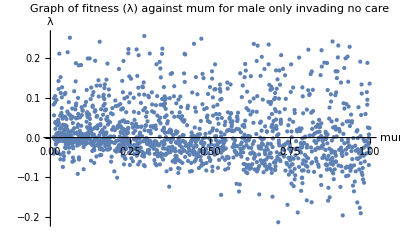

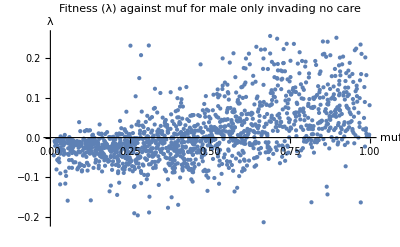

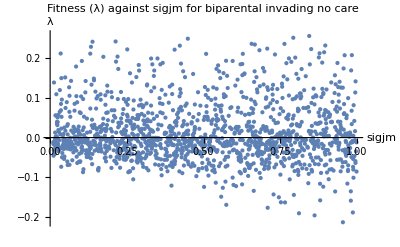

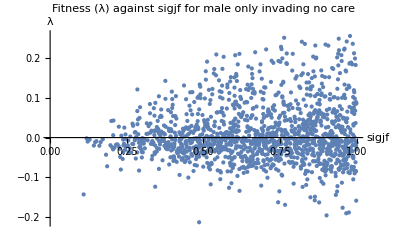

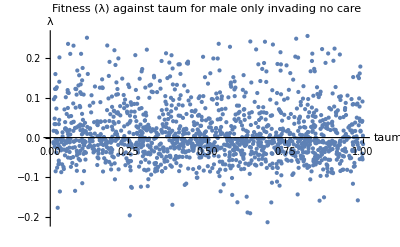

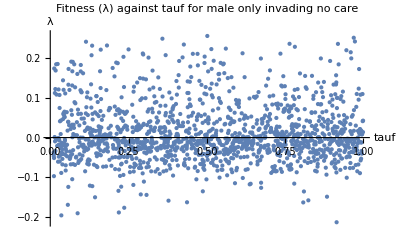

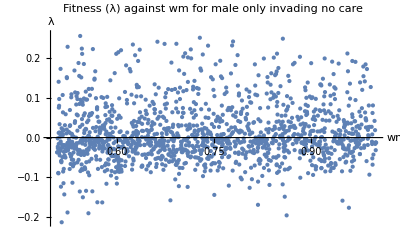

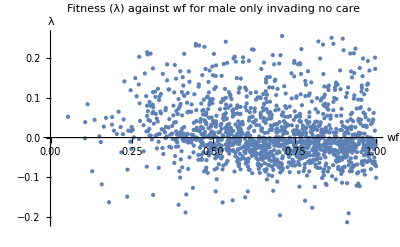

```mathematica
res2hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{mm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res2hpm2 = Select[res2hpm2, # =!= Nothing &];
ListPlot[res2hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Graph of fitness (λ) against mum for male only invading no care",
AxesLabel ->{"mum", "λ"}]


res3hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{mf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res3hpm2 = Select[res3hpm2, # =!= Nothing &];
ListPlot[res3hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against muf for male only invading no care",
AxesLabel ->{"muf", "λ"}]


res4hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{sigjm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res4hpm2 = Select[res4hpm2, # =!= Nothing &];
ListPlot[res4hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against sigjm for biparental invading no care",
AxesLabel ->{"sigjm", "λ"}]


res5hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{sigjf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res5hpm2 = Select[res5hpm2, # =!= Nothing &];
ListPlot[res5hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against sigjf for male only invading no care",
AxesLabel ->{"sigjf", "λ"}]



res6hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{taum[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res6hpm2 = Select[res6hpm2, # =!= Nothing &];
ListPlot[res6hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against taum for male only invading no care",
AxesLabel ->{"taum", "λ"}]

res7hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{tauf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res7hpm2 = Select[res7hpm2, # =!= Nothing &];
ListPlot[res7hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against tauf for male only invading no care",
AxesLabel ->{"tauf", "λ"}]


res8hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{wm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res8hpm2 = Select[res8hpm2, # =!= Nothing &];
ListPlot[res8hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against wm for male only invading no care",
AxesLabel ->{"wm", "λ"}]

res9hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{wf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res9hpm2 = Select[res9hpm2, # =!= Nothing &];
ListPlot[res9hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against wf for male only invading no care",
AxesLabel ->{"wf", "λ"}]

res10hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{k[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res10hpm2 = Select[res10hpm2, # =!= Nothing &];
ListPlot[res10hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against k for male only invading no care",
AxesLabel ->{"k", "λ"}]

res11hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{rr[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res11hpm2 = Select[res11hpm2, # =!= Nothing &];
ListPlot[res11hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against rr for male only invading no care",
AxesLabel ->{"rr", "λ"}]


res12hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{am[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res12hpm2 = Select[res12hpm2, # =!= Nothing &];
ListPlot[res12hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against am for male only invading no care",
AxesLabel ->{"am", "λ"}]


res13hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{af[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res13hpm2 = Select[res13hpm2, # =!= Nothing &];
ListPlot[res13hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against af for male only invading no care",
AxesLabel ->{"af", "λ"}]


res14hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{esm[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res14hpm2 = Select[res14hpm2, # =!= Nothing &];
ListPlot[res14hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against esm for male only invading no care",
AxesLabel ->{"esm", "λ"}]


res15hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{esf[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res15hpm2 = Select[res15hpm2, # =!= Nothing &];
ListPlot[res15hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against esf for male only invading no care",
AxesLabel ->{"esf", "λ"}]

res16hpm2 = Table[
With[{currentAR = AR[[i]]},
If[currentAR >0,
{AR[[i]], λ/. Solve[Det[{{λ+((mum[[i]]*em[[i]]) +(muf[[i]]*ef[[i]]) +(mm[[i]]*esm[[i]])+ (mf[[i]]*esf[[i]])), - rr[[i]]*af[[i]]*(1-(AR[[i]]/k[[i]]))},{-emm[[i]]*sigjm[[i]]*(1-λ*taum[[i]]) - emf[[i]]*sigjf[[i]]*(1-λ*tauf[[i]]), λ+ (wm[[i]]*am[[i]]+ wf[[i]]*af[[i]])}}] ==0, λ][[2]], currentAR},
Nothing
]
],
{i,1,n}
];
res16hpm2 = Select[res16hpm2, # =!= Nothing &];
ListPlot[res16hpm2[[All,{1,2}]], PlotStyle -> PointSize[Small],
PlotLabel ->"Fitness (λ) against AR for male only invading no care",
AxesLabel ->{"AR", "λ"}]
```